```mathematica
Needs["PlotLegends`"]
```

## General

### Run This to browse

```mathematica
Manipulate[plotROC[funcname, xnoise, ynoise, nsamp, nbin],{funcname,Union[functionName/@rocFileNames]}, {xnoise,Union[xNoise/@rocFileNames]}, {ynoise,Union[yNoise/@rocFileNames]}, {nsamp,Union[nSamples/@rocFileNames]}, {nbin,Union[nBins/@rocFileNames]}]
```

## Code

### Data file list

This is the global variable for the filenames containing the roc data. The filenames encode metadata about the contained data.

```mathematica
rocFileNames=FileNames["*.roc.tsv",{"../rocs"}];
```

#### Testing

```mathematica
rocFileNames[[1]]
```

../rocs/00001_parabolic_x000_y000.s005.b001.roc.tsv

```mathematica
rocFileNames[[140]]
```

../rocs/00001_parabolic_x000_y010.s006.b001.roc.tsv

```mathematica
rocFileNames[[440]]
```

../rocs/00001_parabolic_x010_y000.s010.b010.roc.tsv

```mathematica
StringSplit[rocFileNames[[1]],"_"]
```

{../rocs/00001,parabolic,x000,y000.s005.b001.roc.tsv}

### File name metadata extraction

The functions in this section are for extracting metadata from the function names

##### Function name

```mathematica
functionName[filename_String]:=With[{parts=StringSplit[filename,"_"]},
With[{lastPart=Length[parts]-2},
If[lastPart>2,
StringJoin[Flatten[{parts[[2]],{"_",#}&/@parts[[Range[3,lastPart]]]}]],
parts[[2]]]
]]
```

##### Testing

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
{1,a,3,c,5}[[{2,3,4}]]
```

{a,3,c}

```mathematica
functionName["00351_L_x000_y000.s005.b001.roc.tsv"]
```

L

```mathematica
functionName["00351_L_lop_x000_y000.s005.b001.roc.tsv"]
```

L_lop

```mathematica
functionName["00351_Gold_L_lop_x000_y000.s005.b001.roc.tsv"]
```

Gold_L_lop

##### X-axis noise level

```mathematica
xNoise[filename_String]:=With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[split[[Length[split]-1]],1]]/100
]
```

##### Testing

```mathematica
xNoise[rocFileNames[[1]]]
```

0

```mathematica
xNoise[rocFileNames[[440]]]
```

1/10

```mathematica
xNoise["00351_L_lop_x000_y000.s005.b001.roc.tsv"]
```

0

```mathematica
xNoise["00351_L_lop_x010_y000.s005.b001.roc.tsv"]
```

1/10

##### Y-axis noise level

```mathematica
yNoise[filename_String]:=With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[StringSplit[Last[split],"."][[1]],1]]/100]
```

##### Testing

```mathematica
yNoise[rocFileNames[[440]]]
```

0

```mathematica
yNoise[rocFileNames[[140]]]
```

1/10

```mathematica
yNoise["00351_L_lop_x000_y030.s005.b001.roc.tsv"]
```

3/10

```mathematica
yNoise["00351_L_lop_x010_y000.s005.b001.roc.tsv"]
```

0

##### Number of samples

```mathematica
nSamples[filename_String]:=With[{split=StringSplit[filename,"_"]},ToExpression[StringDrop[StringSplit[Last[split],"."][[2]],1]]
]
```

##### Testing

```mathematica
nSamples[rocFileNames[[440]]]
```

10

```mathematica
nSamples[rocFileNames[[140]]]
```

6

##### Number of bins

```mathematica
nBins[filename_String]:=ToExpression[StringDrop[StringSplit[StringSplit[filename,"_"][[4]],"."][[3]],1]]
```

##### Testing

```mathematica
nBins[rocFileNames[[440]]]
```

10

```mathematica
nBins[rocFileNames[[140]]]
```

1

### Plot a single ROC curve

```mathematica
plotROC[funcname_, xnoise_, ynoise_, nsamp_, nbin_]:=With[{filenames=Select[rocFileNames,functionName[#]==funcname&&xNoise[#]==xnoise&&yNoise[#]==ynoise&&nSamples[#]==nsamp&&nBins[#]==nbin&]},If[Length[filenames]==0,"The requested ROC curve has not been calculated",
With[{data=Import[filenames[[1]]]},ListLinePlot[data,PlotRange->All]
]]]
```

#### Testing

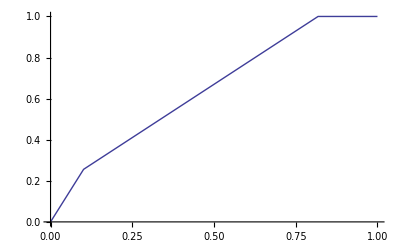

```mathematica
plotROC["parabolic",0,0,6,4]
```

### Plot all mic scores for a given function, noise condition, and number of samples

```mathematica
plotMicROCs[funcname_, xnoise_, ynoise_, nsamp_]:=With[{filenames=Sort[Select[rocFileNames,functionName[#]==funcname&&xNoise[#]==xnoise&&yNoise[#]==ynoise&&nSamples[#]==nsamp&&nBins[#]≥4&],nBins[#1]<nBins[#2]&]},If[Length[filenames]==0,"The requested ROC curves have not been calculated",
With[{data=MapIndexed[Tooltip[#1,nBins[filenames[[#2]][[1]]]]&,Import/@filenames]},
With[{dashStyles={Dashing[{}],Dashed,Dotted,DotDashed},colors=If[Length[data]>1,Table[ColorData["DarkRainbow"][x],{x,0,1,1/(Length[data]-1)}],{Blue}]},
With[{styles=MapIndexed[Directive[#1,dashStyles[[Mod[#2[[1]],Length[dashStyles]]+1]] ]&,colors]},
If[Length[data]>10,
ListLinePlot[data,PlotRange->All,PlotStyle->styles,ImageSize->{1024}],
ListLinePlot[data,PlotRange->All,PlotStyle->styles,ImageSize->{1024},PlotLegend->nBins/@filenames,LegendPosition->{0.8,-0.3}]
]
]]]]]
```

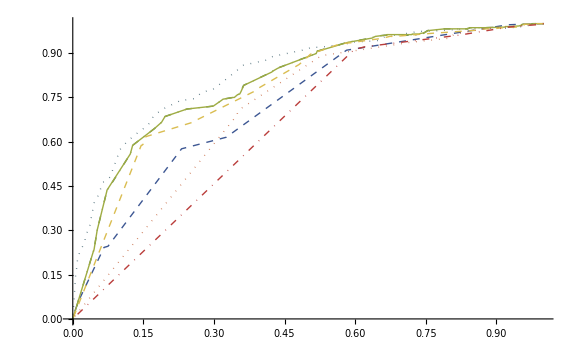

```mathematica
plotMicROCs["parabolic",1/10,1/10,14]
```

```mathematica
Export["foo.svg",plotMicROCs["parabolic",1/10,1/10,12]]
```

foo.svg

```mathematica
Export["foo.png",plotMicROCs["parabolic",1/10,1/10,12]]
```

foo.png

Return number padded on the right with 0's to have places digits

```mathematica
zeroPad[num_,places_]:=ToString[PaddedForm[num,places,NumberPadding->{"0",""},NumberSigns->{"",""}]]
```

```mathematica
exportPlotMicROCs[funcname_, xnoise_, ynoise_, nsamp_]:=With[{destname=funcname<>".x."<>zeroPad[xnoise 100,3]<>".y."<>zeroPad[ynoise 100,3]<>".s."<>zeroPad[nsamp,3]<>".png"},Export[destname,plotMicROCs[funcname,xnoise,ynoise,nsamp]]
]
```

```mathematica
exportPlotMicROCs["parabolic",1/10,1/10,12]
```

parabolic.x.010.y.010.s.012.png

```mathematica
micROCsToExport[]:=With[{
funcs=Union[functionName/@rocFileNames],xnoises=Union[xNoise/@rocFileNames],
ynoises=Union[yNoise/@rocFileNames],
samps=Union[nSamples/@rocFileNames]},
Tuples[{funcs,xnoises,ynoises,samps}]
]
```

```mathematica
Apply[exportPlotMicROCs,#]&/@Take[micROCsToExport[],5]
```

{23halton.x.000.y.000.s.005.svg,23halton.x.000.y.000.s.006.svg,23halton.x.000.y.000.s.007.svg,23halton.x.000.y.000.s.008.svg,23halton.x.000.y.000.s.009.svg}

{{23halton,0,0,5},{23halton,0,0,6},{23halton,0,0,7},{23halton,0,0,8},{23halton,0,0,9}}

```mathematica
Length[Select[micROCsToExport[],#[[4]]<30&]]
```

4212

```mathematica
ParallelMap[Apply[exportPlotMicROCs,#]&,Select[micROCsToExport[],#[[4]]<30&]]
```

Part::partw: Part 3 of x000 does not exist.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[{.

ToExpression::notstrbox: StringDrop[{ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Part::partw: Part 3 of x000 does not exist.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[{.

ToExpression::notstrbox: StringDrop[{ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Part::partw: Part 3 of x000 does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[{.

General::stop: Further output of StringDrop will be suppressed during this calculation.

ToExpression::notstrbox: StringDrop[{ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression will be suppressed during this calculation.

$Aborted

## L-shaped

```mathematica
l10106020=Import["../rocs/00350_L_x010_y010.s060.b020.roc.tsv"];
```

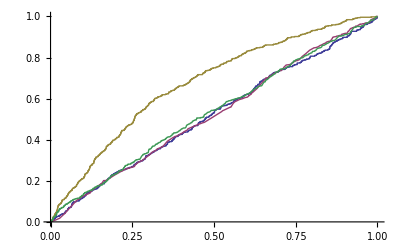

```mathematica
ListLinePlot[{l10106020,l10103018,l10103001,l10103002},PlotLegend->{20,18,"DCor","Spear"},LegendPosition->{0.5,-0.45}]
```

```mathematica
l10103018=Import["../rocs/00350_L_x010_y010.s030.b018.roc.tsv"];
```

```mathematica
l10103001=Import["../rocs/00350_L_x010_y010.s030.b001.roc.tsv"];
```

```mathematica
l10103002=Import["../rocs/00350_L_x010_y010.s030.b002.roc.tsv"];
```

## Parabola w 0.1 0.1 noise

```mathematica
p10106020=Import["../rocs/00001_parabolic_x010_y010.s060.b020.roc.tsv"];
```

```mathematica
p10103018=Import["../rocs/00001_parabolic_x010_y010.s030.b018.roc.tsv"];
```

```mathematica
p10103001=Import["../rocs/00001_parabolic_x010_y010.s030.b001.roc.tsv"];
```

```mathematica
p10103002=Import["../rocs/00001_parabolic_x010_y010.s030.b002.roc.tsv"];
```

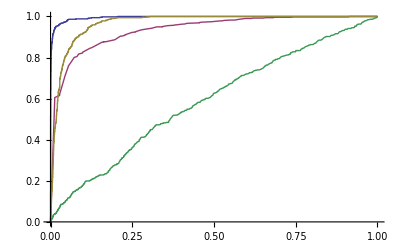

```mathematica
ListLinePlot[{p10106020,p10103018,p10103001,p10103002},PlotRange->All, PlotLegend->{20,18,"DCor","Spear"},LegendPosition->{0.5,-0.45}]
```